# Ixn params

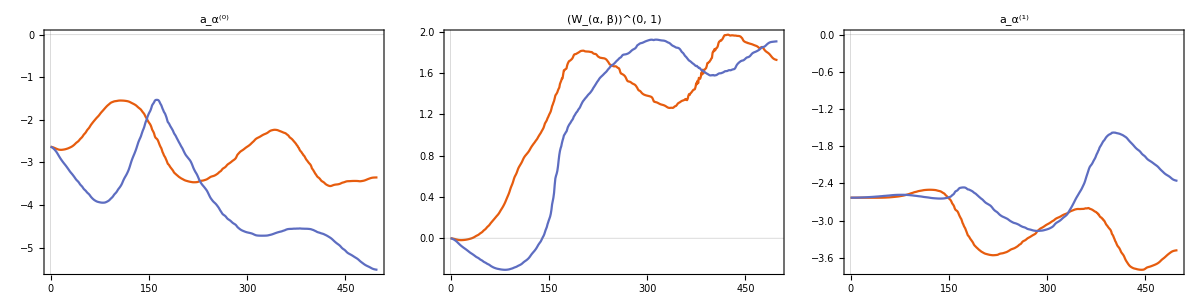

```mathematica
pltIxn=Module[
{ixns},
ixns=Association[];
Do[
ixns[ixn]=Import["../data/"<>dir<>"/ixn_params/"<>ixn<>"_"<>IntegerString[9800,10,5]<>".txt","Table"];
,{ixn,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
Grid[{{
ListLinePlot[{ixns["hX"],ixns["hY"]},PlotRange->All,ImageSize->250,PlotLabel->"a_α^(0)"],
ListLinePlot[{ixns["wXX1"],ixns["wYY1"]},PlotRange->All,ImageSize->250,PlotLabel->"(W_(α, β))^(0, 1)"],
ListLinePlot[{ixns["bX1"],ixns["bY1"]},PlotRange->All,ImageSize->250,PlotLabel->"a_α^(1)"]
}}]
]
```

```mathematica
leg=LineLegend[{ColorData[97,1],ColorData[97,2]},{"H","P"},LabelStyle->Directive[FontSize->20],LegendMarkerSize->40]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/ixns.pdf",pltIxn]
```

figures/ixns.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["figures"],CreateDirectory["figures"]];
Export["figures/ixns_leg.pdf",leg]
```

figures/ixns_leg.pdf

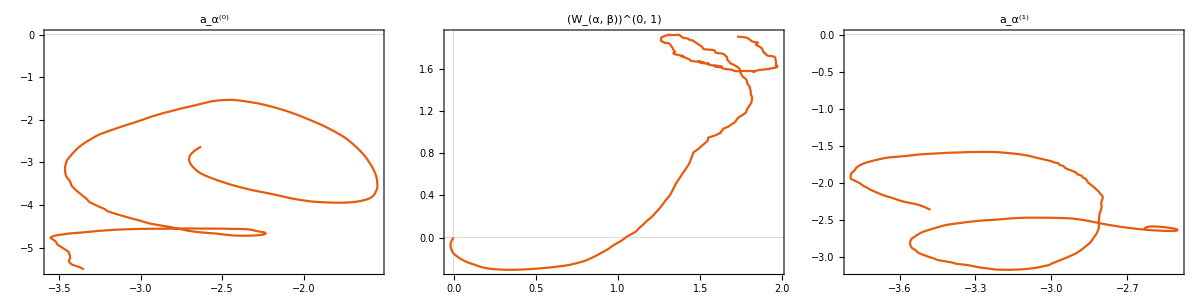

```mathematica
Module[
{ixns},
ixns=Association[];
Do[
ixns[ixn]=Import["../data/"<>dir<>"/ixn_params/"<>ixn<>"_"<>IntegerString[9800,10,5]<>".txt","Table"];
,{ixn,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
Grid[{{
ListLinePlot[Transpose[{ixns["hX"][[;;,2]],ixns["hY"][[;;,2]]}],PlotRange->All,ImageSize->250,PlotLabel->"a_α^(0)"],
ListLinePlot[Transpose[{ixns["wXX1"][[;;,2]],ixns["wYY1"][[;;,2]]}],PlotRange->All,ImageSize->250,PlotLabel->"(W_(α, β))^(0, 1)"],
ListLinePlot[Transpose[{ixns["bX1"][[;;,2]],ixns["bY1"][[;;,2]]}],PlotRange->All,ImageSize->250,PlotLabel->"a_α^(1)"]
}}]
]
```

# Moments

## Calculate and Write Visible

```mathematica
SetDirectory[NotebookDirectory[]];
counts=Association[];
Monitor[
Do[
countsTmp={};
Do[
data=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_"<>IntegerString[sample,10,4]<>".txt","Table"];
AppendTo[countsTmp,{Length[Select[data,#[[3]]=="X"&]],Length[Select[data,#[[3]]=="Y"&]]}];
,{sample,0,100-1}];
counts[timepoint]=Mean[countsTmp]//N;

f=OpenWrite["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_counts.txt"];
WriteString[f,"X "<>ToString[counts[timepoint][[1]]]<>"\n"];
WriteString[f,"Y "<>ToString[counts[timepoint][[2]]]];
Close[f];
,{timepoint,0,500-1}];
,ProgressIndicator[timepoint,{0,500-1}]]
```

## Calculate and Write Hidden

```mathematica
SetDirectory[NotebookDirectory[]];
counts=Association[];
Monitor[
Do[
countsTmp={};
Do[
data=Transpose[Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_"<>IntegerString[sample,10,4]<>".txt","Table"]];
AppendTo[countsTmp,{Total[data[[4]]],Total[data[[6]]]}];
,{sample,0,100-1}];
counts[timepoint]=Mean[countsTmp]//N;

f=OpenWrite["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_counts.txt"];
WriteString[f,"X1 "<>ToString[counts[timepoint][[1]]]<>"\n"];
WriteString[f,"Y1 "<>ToString[counts[timepoint][[2]]]];
Close[f];
,{timepoint,250,500-1}];
,ProgressIndicator[timepoint,{0,500-1}]]
```

## Read visible

```mathematica
countsV=Association[];
Do[
countsV[timepoint]=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_counts.txt","Table"][[;;,2]];
,{timepoint,0,500-1}];
countsV=Values[countsV];
```

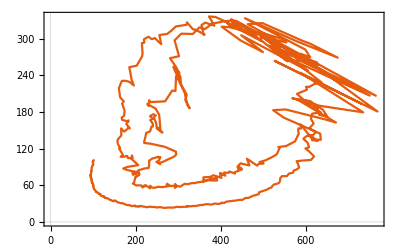

```mathematica
ListLinePlot[countsV]
```

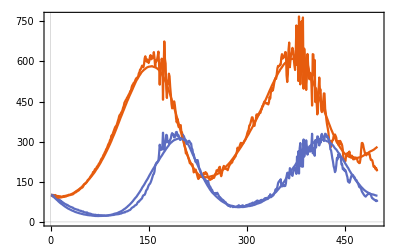

```mathematica
Show[ListLinePlot[Transpose[countsV]],pltMean2]
```

## Read hidden

```mathematica
countsH=Association[];
Do[
countsH[timepoint]=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_counts.txt","Table"][[;;,2]];
,{timepoint,0,500-1}];
countsH=Values[countsH];
```

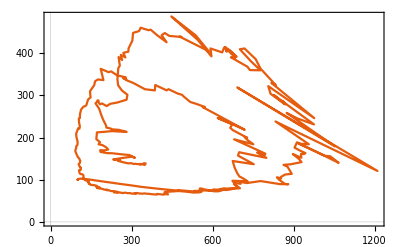

```mathematica
ListLinePlot[countsH]
```

# Time evolution of X moment

```mathematica
boxLength=40;
adj={};
Do[
Do[
idx1=(i1-1)*boxLength+j1;

idx2=idx1;
AppendTo[adj,{idx1,idx2}->1];

i2=i1+1;
j2=j1+1;
If[i2>boxLength,i2=1];
If[j2>boxLength,j2=1];

idx2=(i2-1)*boxLength+j1;
AppendTo[adj,{idx1,idx2}->1];

idx2=(i1-1)*boxLength+j2;
AppendTo[adj,{idx1,idx2}->1];

idx2=(i2-1)*boxLength+j2;
AppendTo[adj,{idx1,idx2}->1];
,{j1,1,boxLength}];
,{i1,1,boxLength}];
adj=SparseArray[adj,{boxLength^2,boxLength^2}];
```

```mathematica
conv[dat_]:=Module[
{datC},
datC=Map[{(#[[1]]-1)*boxLength+#[[2]]}->1&,dat];
Return[SparseArray[datC,{boxLength^2}]];
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
channels=Association[];
channels["hX"]=Association[];
channels["hY"]=Association[];
channels["wXX1"]=Association[];
channels["wYY1"]=Association[];
channels["bX1"]=Association[];
channels["bY1"]=Association[];
xSt=Association[];
Monitor[
Do[
cross=Association[];
cross["hX"]={};
cross["hY"]={};
cross["wXX1"]={};
cross["wYY1"]={};
cross["bX1"]={};
cross["bY1"]={};
means=Association[];
means["hX"]={};
means["hY"]={};
means["wXX1"]={};
means["wYY1"]={};
means["bX1"]={};
means["bY1"]={};
x={};
Do[
data0=Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_0_"<>IntegerString[sample,10,4]<>".txt","Table"];
data1=Transpose[Import["../data/sample_traj/"<>IntegerString[timepoint,10,4]<>"/layer_1_"<>IntegerString[sample,10,4]<>".txt","Table"]];

data0X=conv[Select[data0,#[[3]]=="X"&]];
data0Y=conv[Select[data0,#[[3]]=="Y"&]];
data1X1=data1[[4]];
data1Y1=data1[[6]];

AppendTo[means["hX"],Total[data0X]];
AppendTo[means["hY"],Total[data0Y]];
AppendTo[means["wXX1"],data0X.adj.data1X1];
AppendTo[means["wYY1"],data0Y.adj.data1Y1];
AppendTo[means["bX1"],Total[data1X1]];
AppendTo[means["bY1"],Total[data1Y1]];

AppendTo[x,means["hX"][[-1]]];

Do[
AppendTo[cross[theta],x[[-1]]*means[theta][[-1]]];
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
,{sample,0,100-1}];

Do[
channels[theta][timepoint]=Mean[cross[theta]]-(Mean[means[theta]]*Mean[x])//N;
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
xSt[timepoint]=Mean[x]//N;

f=OpenWrite["../data/channels/mean_X_"<>IntegerString[timepoint,10,4]<>".txt"];
Do[
WriteString[f,theta<>" "<>ToString@AccountingForm[channels[theta][timepoint],{12,10},NumberSigns->{"-",""}]<>"\n"];
,{theta,{"hX","hY","wXX1","wYY1","bX1","bY1"}}];
Close[f];

,{timepoint,0,500-1}];
,ProgressIndicator[timepoint,{0,500-1}]]
```

$Aborted